## Mode equations at small angles for generic coupling

c=1

### Generic angle

#### Zero coupling

The book assumes k[2]=n[2]=0!

```mathematica
(*nv[3]=n Cos[θ];
nv[1]= n Sin[θ];
nv[2]=0;*)
```

Permittivity (for infinitely strong B field):

```mathematica
EqMatrix=ConstantArray[0,{3,3}];ϵ=ConstantArray[0,{3,3}];
```

```mathematica
Do[ϵ[[i]][[j]]=KroneckerDelta[i,j]-ωp^2/(Subscript[γ, c]^3 ω^2(1-nv[3]vp)^2)KroneckerDelta[3,j]KroneckerDelta[3,i],{i,1,3},{j,1,3}];
```

```mathematica
ϵ//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1-ωp^2/(ω^2 (1-vp nv[3])^2 γ_c^3))

```mathematica
Do[EqMatrix[[i]][[j]]=(n^2 KroneckerDelta[i,j]-nv[i]nv[j]-ϵ[[i]][[j]]),{i,1,3},{j,1,3}]
```

```mathematica
Eq=Simplify[Det[EqMatrix]/.nv[1]-> Sqrt[n^2-nv[2]^2-nv[3]^2]/.nv[3]-> n Cos[θ], Assumptions->{θ≥ 0,θ<π}](*/.n-> 1*)
```

((-1+n^2) (ωp^2 (-1+n^2 Cos[θ]^2)-(-1+n^2) ω^2 (-1+n vp Cos[θ])^2 γ_c^3))/(ω^2 (-1+n vp Cos[θ])^2 γ_c^3)

Questa qui sopra dovrebbe esssere la (6.15)..ma non torna! Che e’ sto 3? E questo Sin[2θ]?

#### Generic coupling

Bisogna che il termine con g sia proporzional a E, in modo da aggiungersi alla matrice dei coefficienti. 
Ricavo ϕ dalla seconda Eq in (20) e lo sostituisco nella prima.
Si aggiunge alla posizione (3,3) il termine

```mathematica
newterm=g B 1/ω ϕ /.Solve[B Ez g ω+ω^2(n^2+m^2/ω^2-1)ϕ==0,ϕ]⟦1⟧
```

-(B^2 Ez g^2)/(m^2-ω^2+n^2 ω^2)

```mathematica
EqMatrix[[3]][[3]]+=newterm/Ez;
```

Nuova equazione:

```mathematica
Eqg=Simplify[Det[EqMatrix]/.nv[1]-> Sqrt[n^2-nv[2]^2-nv[3]^2]/.nv[3]-> n Cos[θ], Assumptions->{θ≥ 0,θ<π}]
```

-(((-1+n^2) (-(m^2+(-1+n^2) ω^2) ωp^2 (-2+n^2+n^2 Cos[2 θ])+ω^2 (-1+n vp Cos[θ])^2 (B^2 g^2 (-2+n^2)+2 (-1+n^2) (m^2+(-1+n^2) ω^2)+B^2 g^2 n^2 Cos[2 θ]) γ_c^3))/(2 ω^2 (m^2+(-1+n^2) ω^2) (-1+n vp Cos[θ])^2 γ_c^3))

```mathematica
Simplify[Normal[SeriesCoefficient[Eqg,{g,0,2}]]]
```

-(B^2 (-1+n^2) (-2+n^2+n^2 Cos[2 θ]))/(2 (m^2+(-1+n^2) ω^2))

### Small angle

#### Zero coupling

Since n/=±1 (we are looking for the other modes), we ca divide by (n^2-1)

```mathematica
Eqothers= (1-n^2 - ωp^2/(ω^2 (1-n vp Cos[θ])^2 Subscript[γ, c]^3)(1-n^2 Cos[ θ]^2));
```

```mathematica
Series[(1-n vp Cos[θ])/.vp-> 1-1/(2 Subscript[γ, c]^2),{θ,0,2}]
```

(1-n+n/(2 γ_c^2))+(n/2-n/(4 γ_c^2)) θ^2+O[θ]^3

```mathematica
Series[(1-n Cos[ θ]),{θ,0,2}]
```

(1-n)+(n θ^2)/2+O[θ]^3

```mathematica
Eq620=1-n -((1-n+1/(2 Subscript[γ, c]^2))+(1/2) θ^2)^-2 ωp^2/(ω^2 Subscript[γ, c]^3)((1-n)+θ^2/2);
```

Check:

```mathematica
Eq620-(1-n-(1-n +θ^2/2)ωp^2/(ω^2 Subscript[γ, c]^3)(1-n+1/2(θ^2+Subscript[γ, c]^-2))^-2)//Simplify
```

0

#### Generic coupling

Divide by (1-n^2) again

```mathematica
Eqgothers=Simplify[Eqg/(-1+n^2),Assumptions->{n≠ 1}]
```

1/2 (-(B^2 g^2 (-2+n^2)+2 (-1+n^2) (m^2+(-1+n^2) ω^2)+B^2 g^2 n^2 Cos[2 θ])/(m^2+(-1+n^2) ω^2)+(ωp^2 (-2+n^2+n^2 Cos[2 θ]))/(ω^2 (-1+n vp Cos[θ])^2 γ_c^3))

### Limit Ap>>1 (still working on it)

#### g=0:

```mathematica
Eqgothers/.g-> 0/.vp-> 1//Simplify
```

1-n^2+(ωp^2 (1+n Cos[θ]))/(ω^2 (-1+n Cos[θ]) γ_c^3)

Divide by 1+n:

```mathematica
1-n+ωp^2/(ω^2 (-1+n -θ^2/2) Subscript[γ, c]^3)
```

1-n+ωp^2/((-1+n-θ^2/2) ω^2 γ_c^3)

```mathematica
soln=Solve[1-n+ωp^2/(ω^2 (-1+n -θ^2/2) Subscript[γ, c]^3)==0,n]//Simplify
```

{{n→1/4 (4+θ^2-(√(16 ω^2 ωp^2 γ_c^3+θ^4 ω^4 γ_c^6))/(ω^2 γ_c^3))},{n→1/4 (4+θ^2+(√(16 ω^2 ωp^2 γ_c^3+θ^4 ω^4 γ_c^6))/(ω^2 γ_c^3))}}

```mathematica
(1+θ^2/4-√(SubStar[θ]^4+θ^4))
```

#### All g:

```mathematica
EqgothersAplarge=Eqgothers/.vp-> 1//Simplify
```

-(B^2 g^2 (-2+n^2)+2 (-1+n^2) (m^2+(-1+n^2) ω^2)+B^2 g^2 n^2 Cos[2 θ])/(2 (m^2+(-1+n^2) ω^2))+(ωp^2 (1+n Cos[θ]))/(ω^2 (-1+n Cos[θ]) γ_c^3)

```mathematica
EqgothersAplarge/.g-> 0//Simplify
```

1-n^2+(ωp^2 (1+n Cos[θ]))/(ω^2 (-1+n Cos[θ]) γ_c^3)

```mathematica
D[D[EqgothersAplarge,g],g]/.g-> 0
```

-(2 B^2 (-2+n^2)+2 B^2 n^2 Cos[2 θ])/(2 (m^2+(-1+n^2) ω^2))

Divide by 1+n =(1+n Cos[θ])

```mathematica
EqgothersAplargeThetasmall=1-n+(ωp^2 ((-1+n)-θ^2/2))/(ω^2 ((-1+n)-θ^2/2)^2 Subscript[γ, c]^3)+g^2/2(-(2 B^2 2(n-1-θ^2/2))/(2 (m^2+(-1+n^2) ω^2)))
```

1-n-(B^2 g^2 (-1+n-θ^2/2))/(m^2+(-1+n^2) ω^2)+ωp^2/((-1+n-θ^2/2) ω^2 γ_c^3)

Expand around unperturbed solution

```mathematica
n/.soln⟦1⟧
```

1/4 (4+θ^2-(√(16 ω^2 ωp^2 γ_c^3+θ^4 ω^4 γ_c^6))/(ω^2 γ_c^3))

```mathematica
nexpansion=Simplify[n/.soln⟦1⟧/.Subscript[γ, c]-> (ωp^2/(ω^2 θs^4))^(1/3),Assumptions->{θs>0,ωp>0,ω>0}]+F
```

F+1/4 (4+θ^2-√(θ^4+16 θs^4))

Works for g=0, F=0:

```mathematica
Simplify[SeriesCoefficient[EqgothersAplargeThetasmall/.n-> nexpansion/.Subscript[γ, c]-> (ωp^2/(ω^2 θs^4))^(1/3)/.g-> 0,{F,0,0}],Assumptions->{θs>0,ωp>0,ω>0}]
```

0

```mathematica
solF=Simplify[Solve[Normal[Series[EqgothersAplargeThetasmall/.n-> nexpansion/.Subscript[γ, c]-> (ωp^2/(ω^2 θs^4))^(1/3),{F,0,1}(*,{θ,0,2}*)]]==0,F]⟦1⟧,Assumptions->{θs>0,ωp>0,ω>0,θ>0}];
```

Second order in g:

```mathematica
Simplify[Normal[Series[F/.solF,{g,0,2}]],Assumptions->{θs>0,ωp>0,ω>0,θ>0}]
```

(B^2 g^2 (θ^4+8 θs^4+θ^2 √(θ^4+16 θs^4)))/(2 (1+(16 θs^4)/((θ^2+√(θ^4+16 θs^4))^2)) (m^2 (θ^2+√(θ^4+16 θs^4))+θs^4 (-8-θ^2+√(θ^4+16 θs^4)) ω^2))

```mathematica
(B^2 g^2 (θ^4+8 θs^4+θ^2 G)(θ^2+G)^2)/(2 ((θ^2+G)^2+16 θs^4) (m^2 (θ^2+G)+θs^4 (-8-θ^2+G) ω^2))/.θs-> SubStar[θ]/.G-> G[θ,SubStar[θ]]//Simplify
```

(B^2 g^2 (θ^2+G[θ,θ_*])^2 (θ^4+θ^2 G[θ,θ_*]+8 θ_*^4))/(2 ((θ^2+G[θ,θ_*])^2+16 θ_*^4) (m^2 (θ^2+G[θ,θ_*])+ω^2 (-8-θ^2+G[θ,θ_*]) θ_*^4))

#### In numbers

From Beskin Pjilippov γ=100

```mathematica
Block[{rAminusR=(10^2) ( 10^4 met), B= 10^15 10^-4 kg/(Coul  s), g=10^-11  (10^9 1.602 10^-19 (kg met^2)/s^2)^-1,m= 10^-15 (1.602 10^-19 (kg met^2)/s^2), me= 9.10938356 10^-31 kg(*, α=1/137*)(*, Gauss=10^-4 kg/(Coul /s s^2)*),ne=10^3 10^10 (10^-2 met)^-3,ϵ0=8.854 10^-12 met^-1 s^2 Coul^2/(met^2 kg), e=1.602 10^-19 Coul,c=2.99 10^8 met/s,ℏ=1.055 10^-34 kg met^2/s,ω=2 π 10^9 s^-1,γ=1000,θ=0.1},

Simplify[{(*(g B Sqrt[ϵ0 ℏ^3 c^5])/(ω ℏ), m/(ω ℏ),(θs/.θs-> (ωp^2/(ω^2 γ^3))^(1/4)/.ωp-> Sqrt[e^2 ne / (me ϵ0 )]),*)dispersion=((ϵ0 ℏ^3 c^5) B^2 g^2 (θ^4+8 θs^4+θ^2 √(θ^4+16 θs^4)))/(2 (1+(16 θs^4)/((θ^2+√(θ^4+16 θs^4))^2)) (m^2 (θ^2+√(θ^4+16 θs^4))+θs^4 (-8-θ^2+√(θ^4+16 θs^4)) (ℏ ω)^2))/.θs-> (ωp^2/(ω^2 γ^3))^(1/4)/.ωp-> Sqrt[e^2 ne / (me ϵ0 )],dispersion rAminusR /c},Assumptions->{met>0,s>0,Coul>0,kg>0}]
]
```

{-0.0352727,-0.000117969 s}

```mathematica
kappa=ω((ϵ0 ℏ^3 c^5) B^2 g^2 (θ^4+8 θs^4+θ^2 √(θ^4+16 θs^4)))/(2 (1+(16 θs^4)/((θ^2+√(θ^4+16 θs^4))^2)) (m^2 (θ^2+√(θ^4+16 θs^4))+θs^4 (-8-θ^2+√(θ^4+16 θs^4)) (ℏ ω)^2))/.θs-> (ωp^2/(ω^2 γ^3))^(1/4)/.ωp-> Sqrt[e^2 ne / (me ϵ0 )] //Simplify;
```

```mathematica
inversevel=D[kappa,ω]//Simplify;
```

“Exact” inverse velocity

```mathematica
Block[{rAminusR=(10^2) ( 10^4 met), B= 10^15 10^-4 kg/(Coul  s), g=10^-11  (10^9 1.602 10^-19 (kg met^2)/s^2)^-1,m= 10^-15 (1.602 10^-19 (kg met^2)/s^2), me= 9.10938356 10^-31 kg(*, α=1/137*)(*, Gauss=10^-4 kg/(Coul /s s^2)*),ne=10^3 10^10 (10^-2 met)^-3,ϵ0=8.854 10^-12 met^-1 s^2 Coul^2/(met^2 kg), e=1.602 10^-19 Coul,c=2.99 10^8 met/s,ℏ=1.055 10^-34 kg met^2/s,ω=2 π 10^9 s^-1,γ=1000,θ=0.1},

Simplify[{inversevel(*,dispersion rAminusR /c*)},Assumptions->{met>0,s>0,Coul>0,kg>0}]
]
```

{-0.0330696}

Paolo seems to be right: n is the inverse velocity to a good approximation

```mathematica
Block[{rAminusR=(10^2) ( 10^4 met), B= 10^15 10^-4 kg/(Coul  s), g=10^-11  (10^9 1.602 10^-19 (kg met^2)/s^2)^-1,m= 10^-15 (1.602 10^-19 (kg met^2)/s^2), me= 9.10938356 10^-31 kg(*, α=1/137*)(*, Gauss=10^-4 kg/(Coul /s s^2)*),ne=10^3 10^10 (10^-2 met)^-3,ϵ0=8.854 10^-12 met^-1 s^2 Coul^2/(met^2 kg), e=1.602 10^-19 Coul,c=2.99 10^8 met/s,ℏ=1.055 10^-34 kg met^2/s,ω=omega 2 π 10^9 s^-1,γ=1000,θ=0.1},

inversvelomega=Simplify[{inversevel(*,dispersion rAminusR /c*)},Assumptions->{met>0,s>0,Coul>0,kg>0}];
]
```

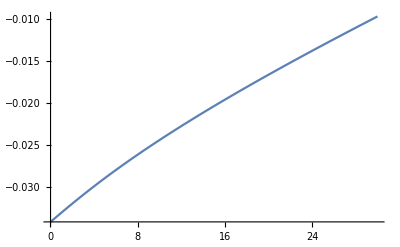

```mathematica
Plot[{inversvelomega/.omega-> 1/Sqrt[x]},{x,0.01,30}(*,PlotRange->{All,{0.0334,0.0342}}*)]
```

### Limit Ap<<1 (still working on it)

#### g=0 (transverse only)

Divide by n+1 and expand for small θ

```mathematica
EqothersAplargeThetasmall=1-n+(ωp^2 (-1+n-θ^2/2) Subscript[γ, c]^-3)/(ω^2 (1-n+1/2(Subscript[γ, c]^-2+θ^2))^2)(*+g^2(-(2 B^2 2(n-1-θ^2/2))/(4 (m^2+(-1+n^2) ω^2)))*)
```

1-n+((-1+n-θ^2/2) ωp^2)/(ω^2 (1-n+1/2 (θ^2+1/γ_c^2))^2 γ_c^3)

```mathematica
Simplify[Normal[Series[EqothersAplargeThetasmall/.Subscript[γ, c]-> ω^2/ωp^2 Ap,{Ap,0,1},{θ,0,2}]]]
```

1-n+4 Ap n-2 Ap (2+θ^2)

```mathematica
Normal[Series[n/.Solve[1-n+4 Ap n-2 Ap (2+θ^2)==0,n]⟦1⟧,{θ,0,2},{Ap,0,1}]]//Simplify
```

1-2 Ap θ^2

#### All g:

```mathematica
EqgothersApsmall=Eqgothers/.vp-> (1-1/(2 Subscript[γ, c]^2))(*/.Subscript[γ, c]-> ω^2/ωp^2 Ap*)//Simplify
```

-(B^2 g^2 (-2+n^2)+2 (-1+n^2) (m^2+(-1+n^2) ω^2)+B^2 g^2 n^2 Cos[2 θ])/(2 (m^2+(-1+n^2) ω^2))+(2 ωp^2 (-2+n^2+n^2 Cos[2 θ]) γ_c)/(ω^2 (n Cos[θ]+(2-2 n Cos[θ]) γ_c^2)^2)

```mathematica
EqgothersApsmall/.g-> 0//Simplify
```

1-n^2+(2 ωp^2 (-2+n^2+n^2 Cos[2 θ]) γ_c)/(ω^2 (n Cos[θ]+(2-2 n Cos[θ]) γ_c^2)^2)

```mathematica
1/2 D[D[EqgothersApsmall,g],g]/.g-> 0
```

-(2 B^2 (-2+n^2)+2 B^2 n^2 Cos[2 θ])/(4 (m^2+(-1+n^2) ω^2))

Divide by n+1 and expand for small θ

```mathematica
EqgothersAplargeThetasmall=1-n+(ωp^2 (-1+n-θ^2/2) Subscript[γ, c]^-3)/(ω^2 (1-n+1/2(Subscript[γ, c]^-2+θ^2))^2)+g^2(-(2 B^2 2(n-1-θ^2/2))/(4 (m^2+(-1+n^2) ω^2)))
```

1-n-(B^2 g^2 (-1+n-θ^2/2))/(m^2+(-1+n^2) ω^2)+((-1+n-θ^2/2) ωp^2)/(ω^2 (1-n+1/2 (θ^2+1/γ_c^2))^2 γ_c^3)

```mathematica
Simplify[Normal[Series[EqgothersAplargeThetasmall/.Subscript[γ, c]-> ω^2/ωp^2 Ap,{Ap,0,0},{θ,0,2}]]]
```

1-n+(B^2 g^2 (2-2 n+θ^2))/(2 (m^2+(-1+n^2) ω^2))

```mathematica
Normal[Series[n/.Solve[1-n+(B^2 g^2 (2-2 n+θ^2))/(2 (m^2(*+(-1+n^2) ω^2*)))==0,n]⟦1⟧,{θ,0,2}(*,{Ap,0,1}*)]](*-(1+(B^2 g^2 θ^2)/(2 (B^2 g^2+m^2)))*)//Simplify
```

1+(B^2 g^2 θ^2)/(2 (B^2 g^2+m^2))